```mathematica
data={{50,0},{60,5},{78,13},{95,16}};
```

```mathematica
line = Fit[data,{1,x},x]
```

-17.0457+0.36107 x

```mathematica
parabola=Fit[data,{1,x,x^2},x]
```

-45.7507+1.1992 x-0.00576977 x^2

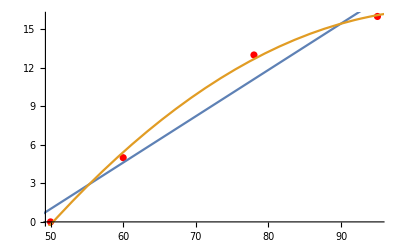

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[{line,parabola},{x,0,100}]]
```

```mathematica
Solve[-45.750747534252405+1.1992018863152796 x-0.0057697743264752965 x^2==16.5,x]
```

{{x→100.685},{x→107.157}}

```mathematica
data={{11.5,85},{-11.5,15},{-26.5,13},{26.5,87},{12.5,86},{-12.5,14},{.5,52},{-.5,48},{1.5,58},{-1.5,42}};
```

```mathematica
cub=Fit[data,{1,x,x^2},x]
```

50.+3.38819 x+9.32455×10^-17 x^2-0.00283951 x^3-5.63055×10^-20 x^4

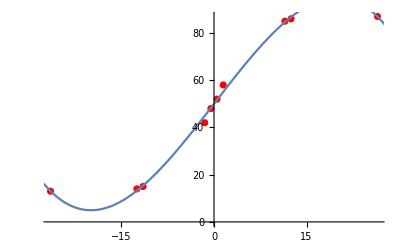

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[cub,{x,-30,30}]]
```